```mathematica
dwarfNum = 20; raBins = 36; decBins = 36;
SetDirectory[NotebookDirectory[]];
BrownData = Import["UltracoolSheetMain.csv"];
headers = First[BrownData]; rows = Rest[BrownData];
(*This beginning part is seperating the header row from the rest of the data we import*)

smallBrownData=rows[[All,{First@First@Position[headers,"name"],First@First@Position[headers,"name_simbadable"],First@First@Position[headers,"ra_j2000_formula"],First@First@Position[headers,"dec_j2000_formula"]}]]
(*This code is taking only the columns with the header names as the strings and making a smaller list with only those 4 headers*)

highValue = {"SDSS J090900.73+652527.2","SDSS J075840.33+324723.4","2MASS J11220826-3512363","SDSS J104829.21+091937.8","SDSS J143553.25+112948.6","SDSS J011912.22+240331.6"}

(*You can change this value if you want to look for specific star names from the CSV file*)
```

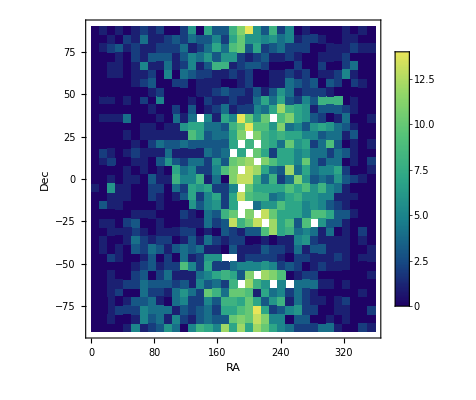

```mathematica
pts = smallBrownData[[All, {3, 4}]];
binSizeRA = 360/36;binSizeDec = 180/36;
RAEdge = Range[0,360, binSizeRA];
DecEdge = Range[-90,90, binSizeDec];
counts = BinCounts[pts, {RAEdge}, {DecEdge}];
CoolColor[ z_ ] :=RGBColor[z,1-z,1];

(*This code above is taking just the RA and Dec parts of our data and assigning it to points, then we choose to break up the celestial sphere into a square with 36 X 36 squares across to find where the stars are most prevelant*)
(*The counts variable uses BinCounts to count up how many BrownDwarfs appear in each square*)

ListDensityPlot[counts, DataRange -> {{0,360},{-90,90}}, FrameLabel-> {"RA", "Dec"}, PlotLegends -> Automatic, ColorFunction ->"BlueGreenYellow", InterpolationOrder -> 0]


(*This Plot shows where the Brown Dwarf Stars are concentrated with the dark blue representing low concentration and the light green/yellow being high*)
```